# Equation Solver for TLN-TDN Project

This notebook solves the relevant equations to obtain the TLN-TDN relations. To achieve this, one first solves the TOV equations to model the background condition. One then solves the perturbation given by equation (29)-(32) in the overleaf document.

## Solving the TOV Equations

```mathematica
ClearAll[K,n,ρ,P, tovEQNs,sol,init, KK];
Exit[]
```

## Equation setup

```mathematica
(*KK=100; (*polytropic constant*)
n=0.5; (*polytropic index*)*)

ρ[r_]:=(P[r]/KK)^(n/(n+1))
```

```mathematica
(*The TOV Equation and the conservation of mass*)
tovEQNs = {m'[r] == 4*Pi*r^2*ρ[r],
P'[r]==-(ρ[r]+P[r])*(m[r]+4 Pi*r^3*P[r])/(r (r-2 m[r])),ν'[r] == (2(m[r]+4*Pi*r^3 P[r]))/(r(r-2m[r]))};
```

```mathematica
(*We then make the quantities dimensionless*)
```

```mathematica
ν[r_] := a0+a1*r+a2*r^2+ a3*r^3 ;
m[r_] := b1*r+b2*r^2 + b3*r^3;
P[r_] := c0+c1*r+c2*r^2+c3*r^3;
```

```mathematica
Expand[tovEQNs[[1]]]
Series[tovEQNs[[1]],{r,0,1}]
```

b1+2 b2 r+3 b3 r^2==4 π r^2 ((c0+c1 r+c2 r^2+c3 r^3)/KK)^(n/(1+n))

b1+2 b2 r+O[r]^2==O[r]^2

```mathematica
Sol=Simplify[Normal[Series[tovEQNs,{r,0,2}]]]
```

{b1+r (2 b2+3 b3 r-4 (c0/KK)^(n/(1+n)) π r)==0,c1+r (2 c2+3 c3 r)==-1/(6 (1-2 b1)^4)(6 (1-2 b1)^2 b2 (c0+(c0/KK)^(n/(1+n)))-(6 b1 (-1+2 b1)^3 c1 (c0+c0 n+(c0/KK)^(n/(1+n)) n))/(c0 (1+n))-(6 b1 (-1+2 b1)^3 (c0+(c0/KK)^(n/(1+n))))/r+1/(c0^2 (1+n)^2)3 (1-2 b1) (-2 (-1+2 b1) b2 c0 c1 (1+n) (c0+c0 n+(c0/KK)^(n/(1+n)) n)+(1-2 b1)^2 b1 (2 c0^2 c2 (1+n)^2+(c0/KK)^(n/(1+n)) n (-c1^2+2 c0 c2 (1+n)))+2 c0^2 (c0+(c0/KK)^(n/(1+n))) (1+n)^2 (2 b2^2-(-1+2 b1) (b3+4 (1-2 b1) c0 π))) r+1/(c0^3 (1+n)^3)(3 (1-2 b1)^2 b2 c0 (1+n) (2 c0^2 c2 (1+n)^2+(c0/KK)^(n/(1+n)) n (-c1^2+2 c0 c2 (1+n)))+(1-2 b1)^3 b1 (6 c0^3 c3 (1+n)^3+(c0/KK)^(n/(1+n)) n (-6 c0 c1 c2 (1+n)+6 c0^2 c3 (1+n)^2+c1^3 (2+n)))+24 c0^3 (c0+(c0/KK)^(n/(1+n))) (1+n)^3 (b2^3-(-1+2 b1)^3 c1 π-(-1+2 b1) b2 (b3+2 (1-2 b1) c0 π))-6 (-1+2 b1) c0^2 c1 (1+n)^2 (c0+c0 n+(c0/KK)^(n/(1+n)) n) (2 b2^2-(-1+2 b1) (b3+4 (1-2 b1) c0 π))) r^2),a1+r (2 a2+3 a3 r)==(2 ((1-2 b1)^3 b1+(1-2 b1)^2 b2 r+(1-2 b1) (2 b2^2-(-1+2 b1) (b3+4 (1-2 b1) c0 π)) r^2+4 (b2^3-(-1+2 b1)^3 c1 π-(-1+2 b1) b2 (b3+2 (1-2 b1) c0 π)) r^3))/((1-2 b1)^4 r)}

```mathematica
Simplify[Normal[Series[Sol[[3]],{r,0,2}]]]/.{b1->0, b2->0}
```

```mathematica
Collect[Simplify[a1+r (2 a2+3 a3 r)-2 ((b3+4 c0 π) r+4 c1 π r^2)],{r,r^2}]
```

a1+(2 a2-2 b3-8 c0 π) r+(3 a3-8 c1 π) r^2

```mathematica
Simplify[Normal[Series[Sol[[2]],{r,0,2}]]]/.{b1->0, b2->0,a1->0}
```

c1+r (2 c2+3 c3 r)==(-6 c0^3 (c0+(c0/KK)^(n/(1+n))) (1+n)^3 (b3+4 c0 π) r^2-(24 c0^3 c1 (c0+(c0/KK)^(n/(1+n))) (1+n)^3 π+6 c0^2 c1 (1+n)^2 (c0+c0 n+(c0/KK)^(n/(1+n)) n) (b3+4 c0 π)) r^3)/(6 c0^3 (1+n)^3 r)

```mathematica
Collect[Simplify[c1+r (2 c2+3 c3 r)==(-6 c0^3 (c0+(c0/KK)^(n/(1+n))) (1+n)^3 (b3+4 c0 π) r^2-(24 c0^3 c1 (c0+(c0/KK)^(n/(1+n))) (1+n)^3 π+6 c0^2 c1 (1+n)^2 (c0+c0 n+(c0/KK)^(n/(1+n)) n) (b3+4 c0 π)) r^3)/(6 c0^3 (1+n)^3 r)],{r,r^2}]/.{c1->0}
```

```mathematica
Solve[Simplify[(b3 c0+2 c2+b3 (c0/KK)^(n/(1+n))+4 c0^2 π+4 c0 (c0/KK)^(n/(1+n)) π) ==0/.b3->KK*(3c0/4π)^(n/n+1)],c2]
```

{{c2→-1/32 c0 (c0+(c0/KK)^(n/(1+n))) π (64+9 c0 KK π)}}

```mathematica
Collect[Normal[Simplify[Series[ν'[r]==-2(P[r]+ρ[r])P'[r],{r,0,2}]]],{r,r^2}]/.c1->0
```

a1+2 (a2+2 c2 (c0+(c0/KK)^(n/(1+n)))) r+(3 a3+6 c3 (c0+(c0/KK)^(n/(1+n)))) r^2==0

## Initial conditions

```mathematica
ϵ=10^-5;(*a small so that singularity may be avoided*)
Pc=10^5; (*central pressure*)
init={m[ϵ]==0,P[ϵ]==Pc, ν[ϵ]=};
```

## TOV Solver

```mathematica
TOVsol=NDSolve[{tovEQNs,init},{P,m},{r,ϵ,1},Method->{"EventLocator","Event"->(P[r]<=0),"EventAction":>"Stop"}];
```

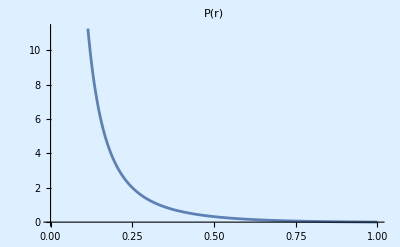

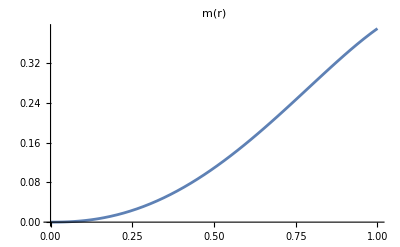

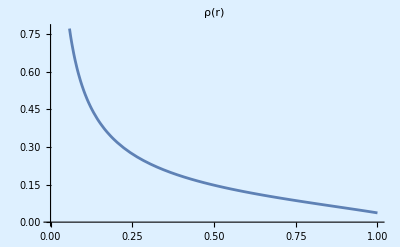

```mathematica
Plot[P[r]/.TOVsol[[1,1]], {r, ϵ, 1},PlotLabel->Style["P(r)", FontFamily->"CMU Classical Serif", FontSize->18, FontColor->Black], Background->LightBlue]
Plot[m[r]/.TOVsol[[1,2]], {r, ϵ, 1},PlotLabel->Style["m(r)", FontFamily->"CMU Classical Serif", FontSize->18, FontColor->Black]]
Plot[ρ[P[r]]/.TOVsol[[1,1]], {r, ϵ, 1},PlotLabel->Style["ρ(r)", FontFamily->"CMU Classical Serif", FontSize->18, FontColor->Black], Background->LightBlue]
```